## Three Neutrino Probabilities in Vacuum

```mathematica
Clear["Global`*"]

(* Definitions *)
Norm2[z_]=Re[z]^2+Im[z]^2;
c12:=Cos[θ12];
c13:=Cos[θ13];
c23:=Cos[θ23];
s12:=Sin[θ12];
s13:=Sin[θ13];
s23:=Sin[θ23];
ots=1.2669327621645516 ; (*constant due to changing parameters *)

(* Experimental data of mixing parameter θ and masses diferrence Δms between flavors 1, 2 and 3 *)
θ23=ArcSin[Sqrt[0.97]]/2;
θ12=ArcSin[Sqrt[0.861]]/2;
θ13=ArcSin[Sqrt[0.1]]/2;
δ=0;
Δms23=0.00232;
Δms12=0.0000759;
```

```mathematica
(* Computing conversion probability (1 -> 2, 1 -> 3) or survival probability (1 -> 1) *)

P[α_,β_,LE_,δ_,θ12_,θ23_,θ13_,Δms12_,Δms23_]=
Block[{U,m1,m2,m3},
m1=0;
m2=Δms12;
m3=Δms12+Δms23;

(* Pontecorvo–Maki–Nakagawa–Sakata matrix U *)
U[k_,j_]:= If[k==1, If[j==1,c13 c12,If[j==2,c13 s12,If[j==3,s13 E^(-I δ)]]], If[k==2,If[j==1,-c23 s12-s13 s23 c12 E^(I δ),If[j==2,c23 c12-s13 s23 s12 E^(I δ),If[j==3,c13 s23]]],If[k==3,If[j==1,s23 s12-s13 c23 c12 E^(I δ),If[j==2,-s23 c12-s13 c23 s12 E^(I δ),If[j==3,c13 c23]]]]]];

Norm2[Sum[Conjugate[U[α,i]] U[β,i] E^(-2 I ots If[i==1,m1,If[i==2,m2,If[i==3,m3,-1]]] LE),{i,1,3}]]];
```

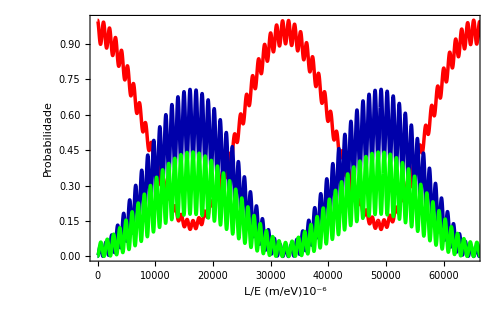

```mathematica
Plot[{P[1,1,LE,δ,θ12,θ23,θ13,Δms12,Δms23],P[1,2,LE,δ,θ12,θ23,θ13,Δms12,Δms23],P[1,3,LE,δ,θ12,θ23,θ13,Δms12,Δms23]},{LE,0,100000},PlotRange->{{0,65000},{0,1}}, PlotPoints->500,PlotStyle->{{Red,Thickness[0.005]},{Darker[Blue],Thickness[0.005]},{Green,Thickness[0.005]}},
Frame->True,FrameLabel->{{"Probabilidade",""},{"L/E (m/eV)10^-6", "Oscilação para um Neutrino Eletrônico"}},
BaseStyle->{FontSize->14,Bold},ImageSize->500]
```